```mathematica
(*探针程序*)
(*========================================================================================================*)
(*========================================================================================================*)
(*start=8;end=start;*)probestotal=4;motiontype="Static/";retype="Re400/";yposition="y=0.3/";case="caseS_re";
path[x_]:=StringReplace["/Users/oc-come/Desktop/CFD/New_Shape/ProbeData/U/"<>motiontype<>yposition<>case<>"δ","δ"->x];
Do[order=ToString[i];
datapre=Import[path[order],"Data"];
datapre=Take[datapre,{probestotal+3,Length@datapre}];
datapre=StringReplace[datapre,{"("->"",")"->""}];
Export["/Users/oc-come/Desktop/CFD/New_Shape/ProbeData/U_Text/"<>motiontype<>yposition<>case<>order<>".txt",datapre],
{i,{253}}];
```

```mathematica
(*Tcut=220;*)(*Tfin=100;*)(*start=8;end=start;*)fig1=fig2=fig3={};probeNo=1;
motiontype="Static/";retype="Re400/";yposition="y=0.3/";(*case="caseS_re";*)
Do[order=ToString[m];
data=ReadList["/Users/oc-come/Desktop/CFD/New_Shape/ProbeData/U_Text/"<>motiontype<>yposition<>case<>order<>".txt",Number,RecordLists->True];
δt=data[[2]][[1]]-data[[1]][[1]];

Tnum1=Ceiling[Tcut/δt];
Tfin=Ttotal=First@data[[Length@data]];
Tnum2=Floor[Tfin/δt];

(*========================================================================================================*)
UxT=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[3*probeNo-1]]}],{j,1,Length@data}]][[2,1]];
UxTcut=Reap[Do[Sow[UxT[[j]]],{j,Tnum1,Tnum2}]][[2,1]];
UyT=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[3*probeNo]]}],{j,1,Length@data}]][[2,1]];
UyTcut=Reap[Do[Sow[UyT[[j]]],{j,Tnum1,Tnum2}]][[2,1]];
(*=========================================================================================================*)
Ux={};
AppendTo[Ux,Table[UxTcut[[j]][[2]],{j,1,Length@UxTcut}]];
Ux=Flatten@Ux;
ccUx=(Max@Ux+Min@Ux)/2;
Do[If[Ux[[i-1]]<ccUx&&Ux[[i+1]]>ccUx&&Abs[Ux[[i]]-ccUx]<10^-3&&Ux[[i]]≥ccUx,stx=i;Break],{i,2,Floor[Length[Ux]/10]-1}];
Do[If[Ux[[i-1]]<ccUx&&Ux[[i+1]]>ccUx&&Abs[Ux[[i]]-ccUx]<10^-2&&Ux[[i]]≤ccUx,enx=i;Break],{i,Ceiling[0.9*Length@Ux]+1,Length@Ux-1}];
Ux=Take[Ux,{stx,enx}];
UxTcut=Take[UxTcut,{stx,enx}];
AveUx=Mean@Ux;
fs=Fourier@Table[UxTcut[[j]][[2]]-AveUx,{j,1,Length[UxTcut]}];
ps=Abs[fs];
max=Max@ps;
ps=Table[{(j-1)/((δt)*Length[UxTcut]),ps[[j]]},{j,1,Length[fs]}];
fre2=First@Select[ps,#[[2]]==max&,1][[1]];
(*==============================================================================================================*)
AmpUx=(Max@Ux-Min@Ux)/2;
lineUx=(Max@Ux+Min@Ux)/2;
T=Reap[Do[If[(UxTcut[[j]][[2]]-lineUx)*(UxTcut[[j+1]][[2]]-lineUx)<0,Sow[Tcut+j*δt]],{j,1,Length@UxTcut-1}]][[2,1]];
If[T=={Null,{}}⟦2,1⟧,frex=fre2;Goto["swag"]];
waveLength=Reap[Do[Sow[T[[j]]-T[[j-1]]],{j,2,Length@T}]][[2,1]];
wave=2*waveLength;
calfre=1/(Mean@wave);
If[NumberQ[calfre],fre1=calfre,fre1="None"];
If[NumberQ[fre1]&&Abs[fre1-fre2]<0.2,frex=fre1,fre=fre2];
Label["swag"];
(*==============================================================================================================*)
(*==============================================================================================================*)
(*==============================================================================================================*)
Uy={};
AppendTo[Uy,Table[UyTcut[[j]][[2]],{j,1,Length@UyTcut}]];
Uy=Flatten@Uy;
ccUy=(Max@Uy+Min@Uy)/2;
Do[If[Uy[[i-1]]<ccUx&&Uy[[i+1]]>ccUy&&Abs[Uy[[i]]-ccUy]<10^-3&&Uy[[i]]≥ccUy,sty=i;Break],{i,2,Floor[Length[Uy]/10]-1}];
Do[If[Uy[[i-1]]<ccUy&&Uy[[i+1]]>ccUy&&Abs[Uy[[i]]-ccUy]<10^-2&&Uy[[i]]≤ccUy,eny=i;Break],{i,Ceiling[0.9*Length@Uy]+1,Length@Uy-1}];
If[NumberQ[sty]==False || NumberQ[eny]==False,Goto[pppy]];
UyTcut=Take[UyTcut,{sty,eny}];
Uy=Take[Uy,{sty,eny}];
AveUy=Mean@Uy;
AmpUy=(Max@Uy-Min@Uy)/2;
Label[pppy];If[NumberQ[sty]==True&&NumberQ[eny]==True,Goto[qqqy]];
Uy={};
AppendTo[Uy,Table[UyTcut[[j]][[2]],{j,1,Length@UyTcut}]];
Uy=Flatten@Uy;
AveUy=Mean@Uy;
AmpUy=(Max@Uy-Min@Uy)/2;
Label[qqqy];

fsy=Fourier@Table[UyTcut[[j]][[2]]-AveUy,{j,1,Length[UyTcut]}];
psy=Abs[fsy];
maxy=Max@psy;
psy=Table[{(j-1)/((δt)*Length[UyTcut]),psy[[j]]},{j,1,Length[fsy]}];
fre2=First@Select[psy,#[[2]]==maxy&,1][[1]];
(*==============================================================================================================*)
AmpUy=(Max@Uy-Min@Uy)/2;
lineUy=(Max@Uy+Min@Uy)/2;
T=Reap[Do[If[(UyTcut[[j]][[2]]-lineUy)*(UyTcut[[j+1]][[2]]-lineUy)<0,Sow[Tcut+j*δt]],{j,1,Length@UyTcut-1}]][[2,1]];
If[T=={Null,{}}⟦2,1⟧,frey=fre2;Goto["swag"]];
waveLength=Reap[Do[Sow[T[[j]]-T[[j-1]]],{j,2,Length@T}]][[2,1]];
wave=2*waveLength;
calfre=1/(Mean@wave);
If[NumberQ[calfre],fre1=calfre,fre1="None"];
If[NumberQ[fre1]&&Abs[fre1-fre2]<0.2,frey=fre1,fre=fre2];
Label["swag"];
(*==============================================================================================================*)
AppendTo[excelU,{case<>order,frex,frey}];
(*AppendTo[fig1,ListLinePlot[UxT,FrameLabel->{"t","Ux"},PlotRange->{All,{-10,10}},Frame->True]];
AppendTo[fig2,ListLinePlot[UxTcut,FrameLabel->{"t","Ux"},PlotRange->{All,{-10,10}},Frame->True]];
AppendTo[fig3,ListLinePlot[ps,FrameLabel->{"Fre","Spe"},PlotLabel->Row[{"Frequency: ",Text@Style[fre,Red]}],Frame->True,PlotRange->{{0,10},All}]],*)
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"UxT/"<>case<>order<>".png",ListLinePlot[UxT,FrameLabel->{"t","Ux"},PlotRange->{All,{-5,5}},Frame->True],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"UxTcut/"<>case<>order<>".png",ListLinePlot[UxTcut,FrameLabel->{"t","Ux"},PlotRange->{All,{-5,5}},Frame->True],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"SpeUx/"<>case<>order<>".png",ListLinePlot[ps,FrameLabel->{"Fre","Spe"},PlotLabel->Row[{"Frequency: ",Text@Style[frex,Red]}],Frame->True,PlotRange->{{0,5},All}],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"UyT/"<>case<>order<>".png",ListLinePlot[UyT,FrameLabel->{"t","Uy"},PlotRange->{All,{-5,5}},Frame->True],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"UyTcut/"<>case<>order<>".png",ListLinePlot[UyTcut,FrameLabel->{"t","Uy"},PlotRange->{All,{-5,5}},Frame->True],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"SpeUy/"<>case<>order<>".png",ListLinePlot[psy,FrameLabel->{"Fre","Spe"},PlotLabel->Row[{"Frequency: ",Text@Style[frey,Red]}],Frame->True,PlotRange->{{0,5},All}],ImageResolution->300],
{m,start,end}]
Clear[st];Clear[en];
(*c=1;
Grid[{{fig1[[c]],fig2[[c]],fig3[[c]]}}]*)
```

Take::take: Cannot take positions 51018 through 564767 in {0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.00192779,0.00192779,0.00192779,0.00192779,«24951»}.

Take::take: Cannot take positions 51018 through 564767 in {{50,0.00192783},{50.002,0.00192783},{50.004,0.00192783},{50.006,0.00192783},{50.008,0.00192783},{50.01,0.00192783},{50.012,0.00192783},{50.014,0.00192783},{50.016,0.00192783},{50.018,0.00192783},{50.02,0.00192783},{50.022,0.00192782},{50.024,0.00192782},{50.026,0.00192782},{50.028,0.00192782},«21»,{50.072,0.0019278},{50.074,0.0019278},{50.076,0.0019278},{50.078,0.0019278},{50.08,0.0019278},{50.082,0.0019278},{50.084,0.0019278},{50.086,0.0019278},{50.088,0.0019278},{50.09,0.0019278},{50.092,0.00192779},{50.094,0.00192779},{50.096,0.00192779},{50.098,0.00192779},«24951»}.

Fourier::fftl: Argument {{50.002-Mean[Take[{0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.00192779,0.00192779,0.00192779,0.00192779,«24951»},«1»]],«1»},«1»} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Take::take: Cannot take positions 2438 through 298500 in {{50,-0.220063},{50.002,-0.220063},{50.004,-0.220063},{50.006,-0.220063},{50.008,-0.220063},{50.01,-0.220063},{50.012,-0.220063},{50.014,-0.220063},{50.016,-0.220063},{50.018,-0.220063},{50.02,-0.220063},{50.022,-0.220063},{50.024,-0.220063},{50.026,-0.220063},{50.028,-0.220063},«21»,{50.072,-0.220063},{50.074,-0.220063},{50.076,-0.220063},{50.078,-0.220063},{50.08,-0.220063},{50.082,-0.220063},{50.084,-0.220063},{50.086,-0.220063},{50.088,-0.220063},{50.09,-0.220063},{50.092,-0.220063},{50.094,-0.220063},{50.096,-0.220063},{50.098,-0.220063},«24951»}.

General::stop: Further output of Take::take will be suppressed during this calculation.

Fourier::fftl: Argument {{50.002-Mean[Take[{-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,-0.220063,«24951»},{2438,298500}]],-0.220063-Mean[«1»]},298500-«1»} is not a non-empty list or rectangular array of numeric quantities.

ListLinePlot::lpn: Take[{{50.,0.00192783},{50.002,0.00192783},{50.004,0.00192783},{50.006,0.00192783},{50.008,0.00192783},{50.01,0.00192783},{50.012,0.00192783},{50.014,0.00192783},{50.016,0.00192783},{50.018,0.00192783},{50.02,0.00192783},{50.022,0.00192782},{50.024,0.00192782},{50.026,0.00192782},«23»,{50.074,0.0019278},{50.076,0.0019278},{50.078,0.0019278},{50.08,0.0019278},{50.082,0.0019278},{50.084,0.0019278},{50.086,0.0019278},{50.088,0.0019278},{50.09,0.0019278},{50.092,0.00192779},{50.094,0.00192779},{50.096,0.00192779},{50.098,0.00192779},«24951»},{51018,564767}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

Fourier::fftl: Argument {{50.002-1. Mean[Take[{0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192783,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192782,0.00192781,0.00192781,«11»,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.00192781,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.0019278,0.00192779,0.00192779,0.00192779,0.00192779,«24951»},«1»]],«1»},«1»} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

```mathematica
excelU
```

{{caseS10,0.785427,1.36291},{caseS7,0.789342,1.37624},{caseS_re190,0.110569,0.21926}}

```mathematica
start=40;end=40;Tcut=50;case="caseS_re";
```

```mathematica
(*pap="/Users/oc-come/Desktop/CFD/POST PROCESS/probes/"
Do[order=ToString[i];
Export[pap<>motiontype<>yposition<>meshtype<>"UxT/"<>casetype<>order<>"(r=0.15).png",fig1[[i-(start-1)]],ImageResolution->300];
Export[pap<>motiontype<>yposition<>meshtype<>"UxTcut/"<>casetype<>order<>"(r=0.15).png",fig2[[i-(start-1)]],ImageResolution->300];
Export[pap<>motiontype<>yposition<>meshtype<>"SpeUx/"<>casetype<>order<>"(r=0.15).png",fig3[[i-(start-1)]],ImageResolution->300],
{i,{10,13,15,16,18,20,22,23,24,25,26,27,29,30,31,32,33,34,35,36,37,38}}]*)
```

```mathematica
Export["/Users/oc-come/Desktop/CFD/New_Shape/excel/MeshTest/Static/Ux/Re400.xlsx",Prepend[excelUx,{"Mesh","FreUx","AmpUx","AveUx"}]]
```

/Users/oc-come/Desktop/CFD/New_Shape/excel/MeshTest/Static/Ux/Re400.xlsx

```mathematica
(*=====================================================================*)
(*=====================================================================*)
(*=====================================================================*)
								(*画所有的图*)
```

```mathematica
excel={};
```

```mathematica
(*Tcut=400;Tfin=500;*)(*start=8;*)fig1=fig2=fig3=fig4=fig5=fig6={};motiontype="Static/";retype="Re200/";
yposition="y=0.3/";
Do[path[x_]:=StringReplace["/Users/oc-come/Desktop/CFD/New_Shape/Cloud/"<>motiontype<>yposition<>case<>"δ","δ"->x];
data={};
order=ToString[m];
data=ReadList[path[order],Number,RecordLists->True];
δt=data[[2]][[1]]-data[[1]][[1]];
Tfin=data[[Length@data]][[1]];
Tnum1=Ceiling[Tcut/δt];
Tnum2=Floor[Tfin/δt];
Ttotal=First@data[[Length[data]]];
(*====================================================================*)
Fxtdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[8]]}],{j,1,Length@data}]][[2,1]];
Fxtdatake=Reap[Do[Sow[Fxtdata[[j]]],{j,Ceiling[Tcut/δt]+1,Tnum2}]][[2,1]];
Fytdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[9]]}],{j,1,Length@data}]][[2,1]];
Fytdatake=Reap[Do[Sow[Fytdata[[j]]],{j,Ceiling[Tcut/δt]+1,Tnum2}]][[2,1]];
FxFydata=Reap[Do[Sow[{data[[j]][[8]],data[[j]][[9]]}],{j,1,Length@data}]][[2,1]];
FxFydatake=Reap[Do[Sow[FxFydata[[j]]],{j,Ceiling[Tcut/δt]+1,Tnum2}]][[2,1]];
Wtdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[16]]}],{j,1,Length@data}]][[2,1]];
Wtdatake=Reap[Do[Sow[Wtdata[[j]]],{j,Ceiling[Tcut/δt]+1,Tnum2}]][[2,1]];
(*====================================================================*)
Fx={};
AppendTo[Fx,Table[Fxtdatake[[j]][[2]],{j,1,Length@Fxtdatake}]];
Fx=Flatten@Fx;
Do[If[Fx[[i-1]]<0&&Fx[[i+1]]>0&&Abs[Fx[[i]]]<10^-3&&Fx[[i]]≥0,st=i;Break],{i,2,Floor[Length[Fx]/10]-1}];
Do[If[Fx[[i-1]]<0&&Fx[[i+1]]>0&&Abs[Fx[[i]]]<10^-3&&Fx[[i]]≤0,en=i;Break],{i,Ceiling[0.9*Length@Fx]+1,Length@Fx-1}];
Fxtdatake=Take[Fxtdatake,{st,en}];
Fx=Take[Fx,{st,en}];
AveFx=Mean@Fx;
AmpFx=(Max@Fx-Min@Fx)/2;
Fy={};
AppendTo[Fy,Table[Fytdatake[[j]][[2]],{j,1,Length@Fytdatake}]];
Fy=Flatten@Fy;
ccy=(Max@Fy+Min@Fy)/2;
Do[If[Fy[[i-1]]<ccy&&Fy[[i+1]]>ccy&&Abs[Fy[[i]]-ccy]<10^-3&&Fy[[i]]≥ccy,sty=i;Break],{i,2,Floor[Length[Fy]/10]-1}];
Do[If[Fy[[i-1]]<ccy&&Fy[[i+1]]>ccy&&Abs[Fy[[i]]-ccy]<10^-3&&Fy[[i]]≤ccy,eny=i;Break],{i,Ceiling[0.9*Length@Fy]+1,Length@Fy-1}];
If[NumberQ[sty]==False || NumberQ[eny]==False,Goto[pppy]];
Fytdatake=Take[Fytdatake,{sty,eny}];
Fy=Take[Fy,{sty,eny}];
AveFy=Mean@Fy;
AmpFy=(Max@Fy-Min@Fy)/2;
Label[pppy];If[NumberQ[sty]==True&&NumberQ[eny]==True,Goto[qqqy]];
Fy={};
AppendTo[Fy,Table[Fytdatake[[j]][[2]],{j,1,Length@Fytdatake}]];
Fy=Flatten@Fy;
AveFy=Mean@Fy;
AmpFy=(Max@Fy-Min@Fy)/2;
Label[qqqy];
(*====================================================================*)
T=Reap[Do[If[Fxtdatake[[j]][[2]]*Fxtdatake[[j+1]][[2]]<0,Sow[Tcut+j*δt]],{j,1,Length@Fxtdatake-1}]][[2,1]];
waveLength=Reap[Do[Sow[T[[j]]-T[[j-1]]],{j,2,Length@T}]][[2,1]];
wave=2*waveLength;
calfre=1/(Mean@wave);
If[NumberQ[calfre],fre1=calfre,fre1="None"];

(*==============================================================================*)
dc=Sum[Fxtdatake[[j]][[2]],{j,1,Length@Fxtdatake}]/Length@Fxtdatake;
fs=Fourier@Table[Fxtdatake[[j]][[2]]-AveFx,{j,1,Length[Fxtdatake]}];
ps=Abs[fs];
max=Max@ps;
ps=Table[{(j-1)/((δt)*Length[Fxtdatake]),ps[[j]]},{j,1,Length[fs]}];
fre2=First@Select[ps,#[[2]]==max&,1][[1]];
If[NumberQ[fre1]&&Abs[fre1-fre2]<0.1,freFx=fre1,freFx=fre2];
psv=Interpolation[ps];

(*===============================================================================*)
W={};
AppendTo[W,Table[Wtdatake[[j]][[2]],{j,1,Length@Wtdatake}]];
W=Flatten@W;
ccw=(Max@W+Min@W)/2;
Do[If[W[[i-1]]<ccw&&W[[i+1]]>ccw&&Abs[W[[i]]-ccw]<10^-3&&W[[i]]≥ccw,stw=i;Break],{i,2,Floor[Length[W]/10]-1}];
Do[If[W[[i-1]]<ccw&&W[[i+1]]>ccw&&Abs[W[[i]]-ccw]<10^-3&&W[[i]]≤ccw,enw=i;Break],{i,Ceiling[0.9*Length@W]+1,Length@W-1}];
If[NumberQ@stw==False||NumberQ@enw==False,Goto[pppw]];
Wtdatake=Take[Wtdatake,{stw,enw}];
W=Take[W,{stw,enw}];
AveW=Mean@W;
AmpW=(Max@W-Min@W)/2;
Label[pppw];If[NumberQ@stw==True&&NumberQ@enw==True,Goto[qqqw]];
W={};
AppendTo[W,Table[Wtdatake[[j]][[2]],{j,1,Length@Wtdatake}]];
W=Flatten@W;
AveW=Mean@W;
AmpW=(Max@W-Min@W)/2;
Label[qqqw];
(*====================================================================*)
dcw=Sum[Wtdatake[[j]][[2]],{j,1,Length@Wtdatake}]/Length@Wtdatake;
fsw=Fourier@Table[Wtdatake[[j]][[2]]-AveW,{j,1,Length[Wtdatake]}];
psw=Abs[fsw];
maxw=Max@psw;
psw=Table[{(j-1)/((δt)*Length[Wtdatake]),psw[[j]]},{j,1,Length[fsw]}];
fre2w=First@Select[psw,#[[2]]==maxw&,1][[1]];

(*-----+++++++++++++++++++++++++++===============================-----------------------------------------------------------------*)
Tw=Reap[Do[If[(Wtdatake[[j]][[2]]-Avew)*(Wtdatake[[j+1]][[2]]-Avew)<0,Sow[Tcut+j*δt]],{j,1,Length@Wtdatake-1}]][[2,1]];
If[Tw=={Null,{}}⟦2,1⟧,freW=fre2w;Goto["swag"]];
waveLengthw=Reap[Do[Sow[Tw[[j]]-Tw[[j-1]]],{j,2,Length@Tw}]][[2,1]];
wavew=2*waveLengthw;
calfrew=1/(Mean@wavew);
If[NumberQ[calfrew],fre1w=calfrew,fre1w="None"];
If[NumberQ[fre1w]&&Abs[fre1w-fre2w]<0.2,freW=fre1w,freW=fre2w];
Label["swag"];
(*====================================================================*)
(*AppendTo[fig1,ListLinePlot[Fxtdata,PlotRange->{All,{-2,2}},AxesLabel->{"t","Fx"}]];
AppendTo[fig2,ListLinePlot[Fxtdatake,PlotRange->{All,{-2,2}},AxesLabel->{"t","Fx"},PlotLabel->Framed[Row[{"AmpFx:",Text@Style[AmpFx,Red],"  ", "AveFx:", Text@Style[AveFx,Red]}]]]];
AppendTo[fig3,ListLinePlot[FxFydatake,PlotRange->All,AxesLabel->{"Fx","Fy"}]];
AppendTo[fig4,ListLinePlot[ps,PlotRange->{{0,5},All},PlotLabel->Framed[Row[{"Fre: ",freFx}]],AxesLabel->{"Fre","Spe"}]];
AppendTo[fig5,ListLinePlot[Wtdatake,PlotRange->{All,{-1,1}},AxesLabel->{"t","W"},PlotLabel->Framed[Row[{"AmpW:",Text@Style[AmpW,Red],"  ", "AveW:", Text@Style[AveW,Red]}]]]];
AppendTo[fig6,ListLinePlot[psw,PlotRange->{{0,5},All},PlotLabel->Framed[Row[{"Fre: ",freW}]],AxesLabel->{"Fre","Spe"}]];*)
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"FxT/"<>case<>order<>".png",ListLinePlot[Fxtdata,PlotRange->{All,{-1,1}},AxesLabel->{"t","Fx"}],ImageResolution->300];
(*====================================================================*)
(*====================================================================*)
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"FxTcut/"<>case<>order<>".png",ListLinePlot[Fxtdatake,PlotRange->{All,{-1,1}},AxesLabel->{"t","Fx"},PlotLabel->Framed[Row[{"AmpFx:",Text@Style[AmpFx,Red],"  ", "AveFx:", Text@Style[AveFx,Red]}]]],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"FyT/"<>case<>order<>".png",ListLinePlot[Fytdata,PlotRange->{All,{-0.2,0.2}},AxesLabel->{"t","Fy"}],ImageResolution->300];
(*====================================================================*)
(*====================================================================*)
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"FyTcut/"<>case<>order<>".png",ListLinePlot[Fytdatake,PlotRange->{All,{-0.2,0.2}},AxesLabel->{"t","Fy"},PlotLabel->Framed[Row[{"AmpFy:",Text@Style[AmpFy,Red],"  ", "AveFy:", Text@Style[AveFy,Red]}]]],ImageResolution->300];
(*====================================================================*)
(*====================================================================*)
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"Fy-Fx/caseS"<>order<>".png",ListLinePlot[FxFydatake,PlotRange->All,AxesLabel->{"Fx","Fy"}],ImageResolution->300];
(*====================================================================*)
(*====================================================================*)
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"SpeFx/"<>case<>order<>".png",ListLinePlot[ps,PlotRange->{{0,5},All},PlotLabel->Framed[Row[{"Fre: ",freFx}]],AxesLabel->{"Fre","Spe"}],ImageResolution->300];
(*====================================================================*)
(*====================================================================*)
(*Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"WTcut/caseS"<>order<>".png",ListLinePlot[Wtdatake,PlotRange->{All,{-1,1}},AxesLabel->{"t","W"},PlotLabel->Framed[Row[{"AmpW:",Text@Style[AmpW,Red],"  ", "AveW:", Text@Style[AveW,Red]}]]],ImageResolution->300];*)
(*====================================================================*)
(*====================================================================*)
(*Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/"<>motiontype<>yposition<>"SpeW/caseS"<>order<>".png",ListLinePlot[psw,PlotRange->{{0,5},All},PlotLabel->Framed[Row[{"Fre: ",freW}]],AxesLabel->{"Fre","Spe"}],ImageResolution->300];*)

(*AveFx1=Sum[Fxtdata[[j]][[2]],{j,1,Length@Fxtdata}]/Length@Fxtdata;*)
(*====================================================================*)
(*AveFx=Sum[Fxtdatake[[j]][[2]],{j,1,Length@Fxtdatake}]/Length@Fxtdatake;*)

(*====================================================================*)
(*AveFx=Sum[Fxtdatake[[j]][[2]],{j,1,Length@Fxtdatake}]/Length@Fxtdatake;*)


AppendTo[excel,{"caseS"<>order,Ttotal,Tcut,AveFx,AmpFx,freFx,AveFy,AmpFy,AveW,AmpW}],
{m,start,end,5}]
(*c=1; 
Grid[{{fig1[[c]],fig2[[c]],fig3[[c]]},{fig4[[c]],fig5[[c]],fig6[[c]]}}]*)
```

Part::partw: Part 1 of {} does not exist.

Take::take: Cannot take positions 23492 through 243173 in {2⟦2⟧,1⟦2⟧}.

ReadList::noopen: Cannot open /Users/oc-come/Desktop/CFD/New_Shape/Cloud/Static/y=0.3/caseS_re215.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification Symbol⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

First::normal: Nonatomic expression expected at position 1 in First[Symbol].

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Do::iterb: Iterator {j,Ceiling[Tcut/δt]+1,Tnum2} does not have appropriate bounds.

General::stop: Further output of Do::iterb will be suppressed during this calculation.

Take::take: Cannot take positions 23492 through 243173 in {Do[Sow[Fxtdata⟦j⟧],{j,Ceiling[Tcut Power[«2»]]+1,Tnum2}],{}}⟦2,1⟧.

Take::take: Cannot take positions 23492 through 243173 in {2⟦2⟧,1⟦2⟧}.

General::stop: Further output of Take::take will be suppressed during this calculation.

Mean::rectt: Rectangular array expected at position 1 in Mean[{{2 (2-Null),{}},-2}].

Fourier::fftl: Argument {2-Mean[Take[{2⟦2⟧,1⟦2⟧},{23492,243173}]],243173-Mean[Take[{2⟦2⟧,1⟦2⟧},{23492,243173}]]} is not a non-empty list or rectangular array of numeric quantities.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Interpolation::indat: Data point {Indeterminate,Fourier[{2-Mean[Take[{«2»},{«2»}]],243173-Mean[Take[{«2»},{«2»}]]}]} contains abscissa Indeterminate, which is not a real number.

Fourier::fftl: Argument {{},1/2 (-1⟦2⟧-2⟦2⟧)+2⟦2⟧,1⟦2⟧+1/2 (-1⟦2⟧-2⟦2⟧)} is not a non-empty list or rectangular array of numeric quantities.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

ListLinePlot::lpn: {Null,{}}⟦2,1⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Fourier::fftl: Argument {2.-1. Mean[Take[{2.⟦2⟧,1.⟦2⟧},{23492,243173}]],243173.-1. Mean[Take[{2.⟦2⟧,1.⟦2⟧},{23492,243173}]]} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

```mathematica
excel
```

{{caseS4,600.,300,0.00212377,0.0390598,0.157904,-0.0999318,0.00342707,0.,0.},{caseS4,600.,300,0.00212377,0.0390598,0.157904,-0.0999318,0.00342707,0.,0.},{caseS40,First[Symbol],50,Mean[Take[{2⟦2⟧,1⟦2⟧},{23492,243173}]],0,{},Mean[Take[{2⟦2⟧,1⟦2⟧},{2438,298500}]],0,1/2 (1⟦2⟧+2⟦2⟧),1/2 (Max[1⟦2⟧,2⟦2⟧]-Min[1⟦2⟧,2⟦2⟧])},{caseS210,400.,150,-0.0000557426,0.00957956,0.118332,-0.0845854,0.000496125,0.,0.},{caseS215,First[Symbol],150,Mean[Take[{2⟦2⟧,1⟦2⟧},{23492,243173}]],0,{},Mean[Take[{2⟦2⟧,1⟦2⟧},{21131,248871}]],0,1/2 (1⟦2⟧+2⟦2⟧),1/2 (Max[1⟦2⟧,2⟦2⟧]-Min[1⟦2⟧,2⟦2⟧])},{caseS220,300.,150,-0.0000659491,0.0158863,0.128652,-0.0899965,0.00092742,0.,0.},{caseS225,300.,150,-0.000083073,0.0180267,0.133209,-0.0910809,0.00105493,0.,0.},{caseS230,400.,150,0.00145084,0.0212135,0.143228,-0.101707,0.00139905,0.,0.},{caseS235,300.,150,-0.00197903,0.0258687,0.144769,-0.0950776,0.00204246,0.,0.},{caseS240,300.,150,-0.00258143,0.0292181,0.147271,-0.0965537,0.00241782,0.,0.},{caseS245,300.,150,-0.00311713,0.0355538,0.151176,-0.0985173,0.00289594,0.,0.}}

```mathematica
excel={};
```

```mathematica
Tcut=150;(*Tfin=200;*)start=210;end=245;case="caseS_re";
```

```mathematica
(*Do[order=ToString[i];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/MeshTest/"<>motiontype<>retype<>"FxT/Mesh"<>order<>".png",fig1[[i-(start-1)]],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/MeshTest/"<>motiontype<>retype<>"FxTcut/Mesh"<>order<>".png",fig2[[i-(start-1)]],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/MeshTest/"<>motiontype<>retype<>"Fy-Fx/Mesh"<>order<>".png",fig3[[i-(start-1)]],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/MeshTest/"<>motiontype<>retype<>"SpeFx/Mesh"<>order<>".png",fig4[[i-(start-1)]],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/MeshTest/"<>motiontype<>retype<>"WTcut/Mesh"<>order<>".png",fig5[[i-(start-1)]],ImageResolution->300];
Export["/Users/oc-come/Desktop/CFD/New_Shape/PostProcess/MeshTest/"<>motiontype<>retype<>"SpeW/Mesh"<>order<>".png",fig6[[i-(start-1)]],ImageResolution->300],{i,{1}}]*)
```

```mathematica
Export["/Users/oc-come/Desktop/CFD/New_Shape/excel/"<>motiontype<>"F_yspere=0.3.xlsx",Prepend[excel,{"case","totalT(s)","Tcut(s)","AveFx","AmpFx","FreFx","AveFy","AmpFy","AveW","AmpW"}]]
```

/Users/oc-come/Desktop/CFD/New_Shape/excel/Static/F_yspere=0.3.xlsx

```mathematica
0.31707095-
```

```mathematica
ckc={};fig={};
```

```mathematica
(*=++++++++++============+++++++++++++++==========++++++++++++++++==========-------——————————————*)
(*=++++++++++============+++++++++++++++==========++++++++++++++++==========-------——————————————*)
(*=++++++++++============+++++++++++++++==========++++++++++++++++==========-------——————————————*)
                                                                                     (*探针线程序*)
motiontype="Static/";retype="Re200/";r=0.2;Yc=1;
f[x_]:=StringReplace["/Users/oc-come/Desktop/CFD/New_Shape/ProbeData/Single_Graph/MeshTest/"<>motiontype<>retype<>"Meshδ/40/line_U.xy",{"δ"->x}];
Do[order=ToString[i];
data=ReadList[f[order],Number,RecordLists->True];
UYT=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[3]]}],{j,1,Length@data}]][[2,1]];
Y=Interpolation[UYT];
t1=(*y/.First@FindRoot[Y[y],{y,0.5}]*)r+Yc;
t2=y/.First@FindRoot[Y[y],{y,5,10}];
Which[t1≠t2&&Abs[t2-t1]>0.7,lenY=Text@Style[Abs[t2-t1],Green],t1==t2||Abs[t2-t1]≤0.7,lenY=Text@Style["not satisfied in 2",Red]];
AppendTo[ckc,lenY];
AppendTo[fig,ListLinePlot[UYT,PlotRange->All(*PlotLegends->Placed[{Framed[Text@Style["case"<>order<>"'s length is "ckc[[i]],White],FrameStyle->Orange,Background->Black]},Above]*)]],
{i,{1,1.5,2,2.5}}];


ckc
```

{5.49454,5.51543,5.51683,5.52508}

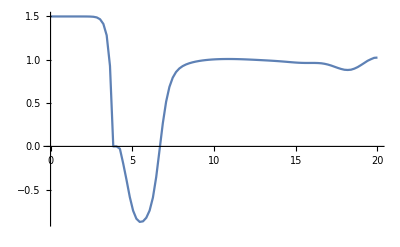
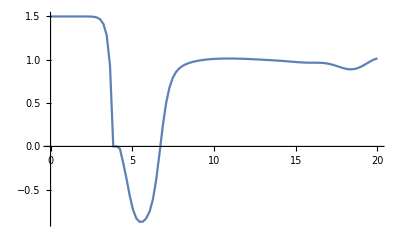
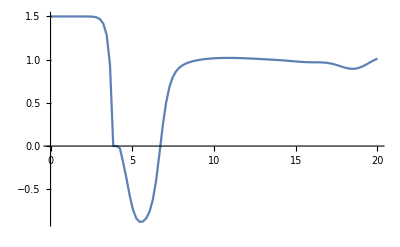
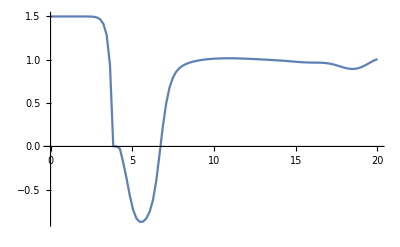

```mathematica
fig
```

```mathematica
len1=5.67312;len1.5=5.7074;len2=5.71082;len2.5=5.39107;
```

Set::write: 0.5 5.67312 中的标签 Times 被保护.

Set::write: 0.5 5.71082 中的标签 Times 被保护.

```mathematica
Row[Framed/@{Column[Table[Text["case"<>ToString[i]],{i,1,10}]],Column[ck1],Column[ck2],Column[ck3]}]
```

```mathematica
Row[Framed/@{Column[Table[Text["case"<>ToString[i]],{i,21,21}]],Column[ck1],Column[ck2],Column[ck3]}]
```

case211.390781.36219Column[ck3]